```mathematica
S10={-3,-6,-1};
S20={-4,-6,-3};
J0={0,0,12};
S0=S10+S20;
L0=J0-S0;
J=Norm[J0];
L=Norm[L0]//N;
```

```mathematica
SolveAndSortRoots[J_,L_,ξ_]:=Module[{roots},
roots=NSolve[x^3+J x^2+L x+ξ==0,x];
roots=x/. roots//Simplify;
Sort[roots]]
```

```mathematica
I3[x_]:=(x[[3]]-x[[1]])/(x[[3]]-x[[2]]);

DI3[J_,L_,ξ_]:=Module[{x,ratio,derivative},
x=SolveAndSortRoots[J,L,ξ];
ratio=I3[x];
derivative=D[ratio,ξ];
derivative]
```

```mathematica
RetrieveDerivative[J_,L_,ξ_]:=Module[{case,derivative},
derivative=I3[J,L,ξ];
derivative]
```

```mathematica
PlotDerivative[J_,L_,ξMin_,ξMax_]:=Plot[RetrieveDerivative[J,L,ξ],{ξ,ξMin,ξMax},AxesLabel->{"ξ","dI_3/dξ"}]
```

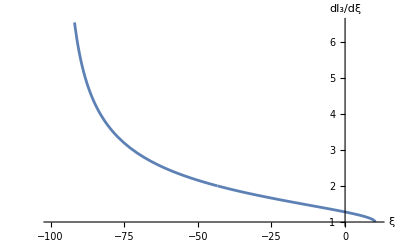

```mathematica
PlotDerivative[J,L,-100,11]
```